```mathematica
SetDirectory[NotebookDirectory[]];
a1=Import["y_act1.csv","Data"];
a1=ArrayReshape[a1,{20,20,100,4}];
a2=Import["y_act2.csv","Data"];
a2=ArrayReshape[a2,{20,20,100,4}];
l1=Import["y_predL1.csv","Data"];
l1=ArrayReshape[l1,{20,20,100,4}];
l2=Import["y_predL2.csv","Data"];
l2=ArrayReshape[l2,{20,20,100,4}];
m1=Import["y_predM1.csv","Data"];
m1=ArrayReshape[m1,{20,20,100,4}];
m2=Import["y_predM2.csv","Data"];
m2=ArrayReshape[m2,{20,20,100,4}];
x1=Import["y_predX1.csv","Data"];
x1=ArrayReshape[x1,{20,20,100,4}];
x2=Import["y_predX2.csv","Data"];
x2=ArrayReshape[x2,{20,20,100,4}];
```

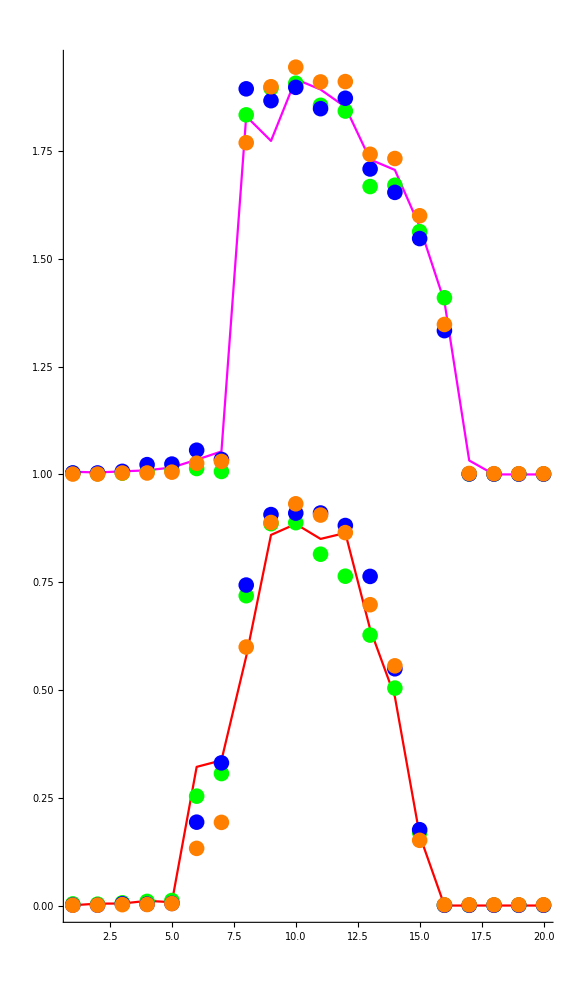

```mathematica
m=75;
n=1;
Show[ListLinePlot[a1[[All,20,m,n]],PlotStyle->Red],
ListPlot[l1[[All,20,m,n]],PlotStyle->Green],
ListPlot[m1[[All,20,m,n]],PlotStyle->Blue],
ListPlot[x1[[All,20,m,n]],PlotStyle->Orange],
ListLinePlot[1+a2[[All,20,m,n]],PlotStyle->Magenta],
ListPlot[1+l2[[All,20,m,n]],PlotStyle->Green],
ListPlot[1+m2[[All,20,m,n]],PlotStyle->Blue],
ListPlot[1+x2[[All,20,m,n]],PlotStyle->Orange],
PlotRange->All,AspectRatio->1.75,FrameStyle->Directive[Red,Dotted],FrameLabel->"Chirality",ImageSize->Large]
```

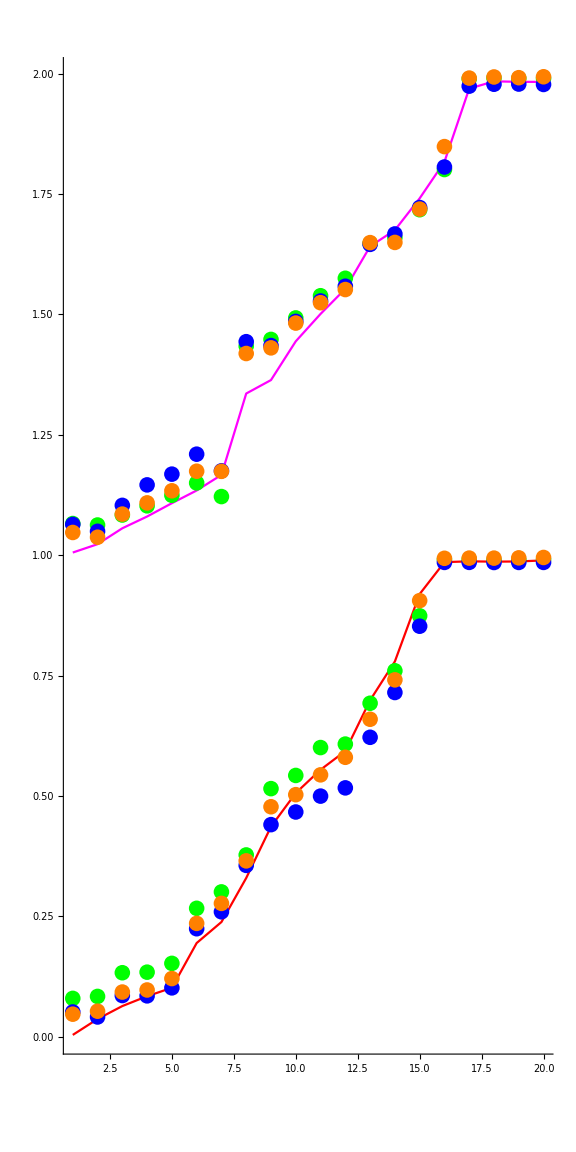

```mathematica
m=75;
n=2;
Show[ListLinePlot[a1[[All,20,m,n]],PlotStyle->Red],
ListPlot[l1[[All,20,m,n]],PlotStyle->Green],
ListPlot[m1[[All,20,m,n]],PlotStyle->Blue],
ListPlot[x1[[All,20,m,n]],PlotStyle->Orange],
ListLinePlot[1+a2[[All,20,m,n]],PlotStyle->Magenta],
ListPlot[1+l2[[All,20,m,n]],PlotStyle->Green],
ListPlot[1+m2[[All,20,m,n]],PlotStyle->Blue],
ListPlot[1+x2[[All,20,m,n]],PlotStyle->Orange],
PlotRange->All,AspectRatio->2,FrameStyle->Directive[Red,Dotted],FrameLabel->"Chirality",ImageSize->Large]
```

10

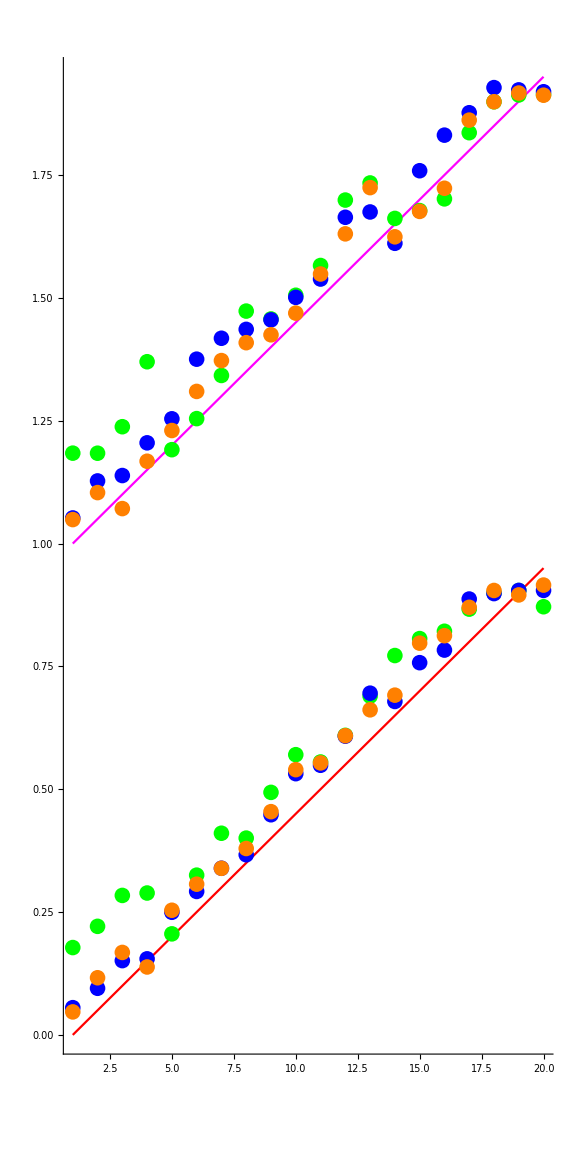

```mathematica
m=75;
n=3;
T=10
Show[ListLinePlot[a1[[All,T,m,n]],PlotStyle->Red],
ListPlot[l1[[All,T,m,n]],PlotStyle->Green],
ListPlot[m1[[All,T,m,n]],PlotStyle->Blue],
ListPlot[x1[[All,T,m,n]],PlotStyle->Orange],
ListLinePlot[1+a2[[All,T,m,n]],PlotStyle->Magenta],
ListPlot[1+l2[[All,T,m,n]],PlotStyle->Green],
ListPlot[1+m2[[All,T,m,n]],PlotStyle->Blue],
ListPlot[1+x2[[All,T,m,n]],PlotStyle->Orange],
PlotRange->All,AspectRatio->2,FrameStyle->Directive[Red,Dotted],FrameLabel->"Chirality",ImageSize->Large]
```

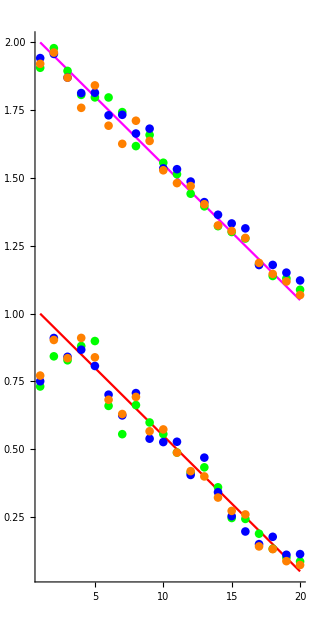

```mathematica
m=75;
n=4;
B=10;
Show[ListLinePlot[a1[[B,All,m,n]],PlotStyle->Red],
ListPlot[l1[[B,All,m,n]],PlotStyle->Green],
ListPlot[m1[[B,All,m,n]],PlotStyle->Blue],
ListPlot[x1[[B,All,m,n]],PlotStyle->Orange],
ListLinePlot[1+a2[[B,All,m,n]],PlotStyle->Magenta],
ListPlot[1+l2[[B,All,m,n]],PlotStyle->Green],
ListPlot[1+m2[[B,All,m,n]],PlotStyle->Blue],
ListPlot[1+x2[[B,All,m,n]],PlotStyle->Orange],
PlotRange->All,AspectRatio->2,FrameStyle->Directive[Red,Dotted],FrameLabel->"Chirality"]
```